```mathematica
h[x_]:=Piecewise[{{1+Subscript[c, 0,1] x+Subscript[c, 0,2] x^2+Subscript[c, 0,3] x^3, 0≤x≤1}, {Subscript[c, 1,1](x-1)+Subscript[c, 1,2](x-1)^2+Subscript[c, 1,3](x-1)^3, 1<x≤2}, {0, True}}];
f[x_]:=h[Abs[x]];
AllVars={Subscript[c, 0,1],Subscript[c, 0,2],Subscript[c, 0,3],Subscript[c, 1,1],Subscript[c, 1,2],Subscript[c, 1,3]};
```

```mathematica
(*Interpolant constraints*)
I1=f[1]
I2=f[2]
```

1+c_(0,1)+c_(0,2)+c_(0,3)

c_(1,1)+c_(1,2)+c_(1,3)

```mathematica
(*Partition of unity and linear term*)
T0=CoefficientList[FullSimplify[∑_(k=-1)^2 f[x-k],x>0&&x<1],x]
T1=CoefficientList[FullSimplify[∑_(k=-1)^2 k f[x-k],x>0&&x<1],x]
```

{2+c_(0,1)+c_(0,2)+c_(0,3)+c_(1,1)+c_(1,2)+c_(1,3),-2 c_(0,2)-3 c_(0,3)-2 c_(1,2)-3 c_(1,3),2 c_(0,2)+3 c_(0,3)+2 c_(1,2)+3 c_(1,3)}

{1+c_(0,1)+c_(0,2)+c_(0,3)+2 c_(1,1)+2 c_(1,2)+2 c_(1,3),-c_(0,1)-2 c_(0,2)-3 c_(0,3)-3 c_(1,1)-4 c_(1,2)-6 c_(1,3),c_(0,2)+3 c_(0,3)+c_(1,2)+6 c_(1,3),-c_(0,3)-3 c_(1,3)}

```mathematica
GenSols=Solve[{
	I1==0,
	I2==0,
	T0[[1]]==1,
	T0[[2]]==0,
	T0[[3]]==0,
	T1[[1]]==0,
	T1[[2]]==1,
	T1[[3]]==0,
	T1[[4]]==0
	},
	AllVars
]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c_(0,3)→-1-c_(0,1)-c_(0,2),c_(1,1)→-4/3-(4 c_(0,1))/3-(c_(0,2))/3,c_(1,2)→1+c_(0,1),c_(1,3)→1/3+(c_(0,1))/3+(c_(0,2))/3}}

```mathematica
RegionXY[k_]:={Quotient[k,2],1+Quotient[-k,2]};
Regions=Table[RegionXY[k],{k,-2,5}]
```

{{-1,2},{-1,1},{0,1},{0,0},{1,0},{1,-1},{2,-1},{2,-2}}

```mathematica
GenSol=GenSols[[1]];
f[x_,y_]:=f[x]f[y];
W[k_]:=Piecewise[{{0, k<0}, {φ^2/2, k==0}, {1-(1-φ)^2/2, k==1}, {1, True}}];
SumF=∑_(i=-3)^5 ∑_(j=-3)^5 W[i-j]f[x-i,y-j]/.GenSol;
SimplifySquare[f_,x0_,y0_]:=Simplify[f,x>x0&&x<x0+1&&y>y0&&y<y0+1];
DSimplifySquare[f_,{x0_,y0_}]:=Simplify[D[SimplifySquare[f,x0,y0],{{x,y}}]];
DSumF=ParallelMap[DSimplifySquare[SumF,#]&,Regions];
```

```mathematica
AnisoInt[df_,{x0_,y0_}]:=Simplify[Integrate[Expand[(df.{1,1})^2],{x,x0,x0+1},{y,y0,y0+1}]];
AnisoInts=Parallelize[MapThread[AnisoInt,{DSumF,Regions}]];
Err=Simplify[Total[AnisoInts]/.φ->1/2]
```

1/907200(2073435+630023 c_(0,1)^4+2452640 c_(0,2)+998496 c_(0,2)^2+153882 c_(0,2)^3+8351 c_(0,2)^4+4 c_(0,1)^3 (949251+211676 c_(0,2))+6 c_(0,1)^2 (1366684+649053 c_(0,2)+71515 c_(0,2)^2)+4 c_(0,1) (1745927+1424046 c_(0,2)+334644 c_(0,2)^2+24320 c_(0,2)^3))

```mathematica
FreeVars=Variables[Err];
DErr=Simplify[D[Err,{FreeVars}]];
H=D[DErr,{FreeVars}];
Sols=RootReduce[Solve[DErr==0,FreeVars,Reals]];
RootReduce[Sols[[1]]]
TableForm[{Range[Length[Sols]],Err/.N[Sols],PositiveDefiniteMatrixQ[H/.N[#]]&/@Sols}ᵀ]
```

{c_(0,1)→Root[11136212089427417799940+40565503933508466119319 #1+56175410802925780786716 #1^2+41251698626094358074618 #1^3+18239143335129521212776 #1^4+5173229177780774994150 #1^5+956712737540209331904 #1^6+112632888717491520636 #1^7+7734928656195327168 #1^8+239273075197171456 #1^9&,1],c_(0,2)→Root[3374023697485280698110075+8537532930936839854857150 #1-1103781936366867775279410 #1^2+951787233357756794329620 #1^3-383780785728198277951170 #1^4+81595240042195026782580 #1^5-9947775659359580484972 #1^6+712083875694813372936 #1^7-28030349234173638144 #1^8+478546150394342912 #1^9&,1]}

1 | 0.0494529 | True

{c_(0,3)→-0.00469238,c_(1,1)→-0.377073,c_(1,2)→0.375509,c_(1,3)→0.00156413,c_(0,1)→-0.624491,c_(0,2)→-0.370817}

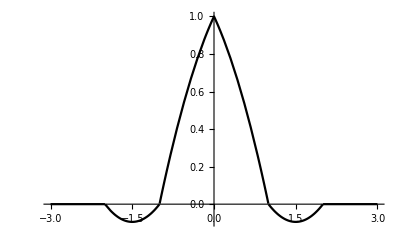

```mathematica
NSol=N[Sols[[1]]];
FullSol=Join[GenSol/.NSol,NSol]
fo[x_]:=f[x]/.FullSol;
Plot[fo[x],{x,-3,3},PlotStyle->Black,Background->White]
```